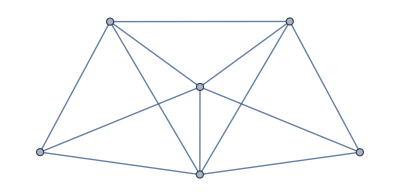
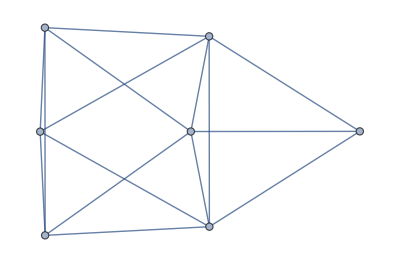
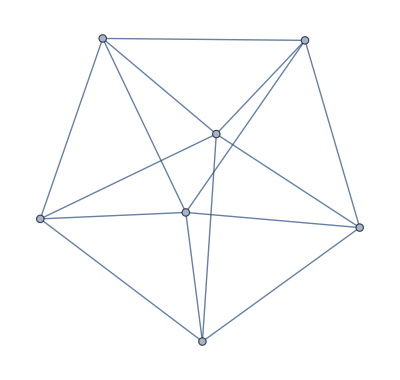

```mathematica
Select[Table[ReadGrof[k],{k,15}],Max[VertexDegree[#]]==5&]
```

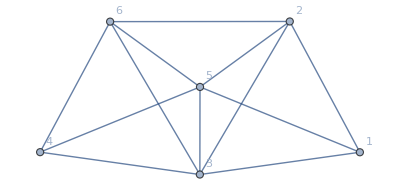
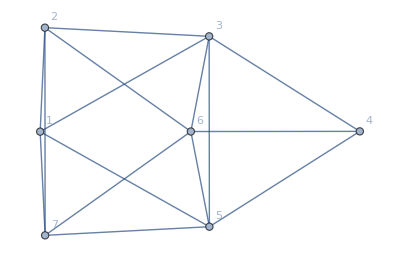
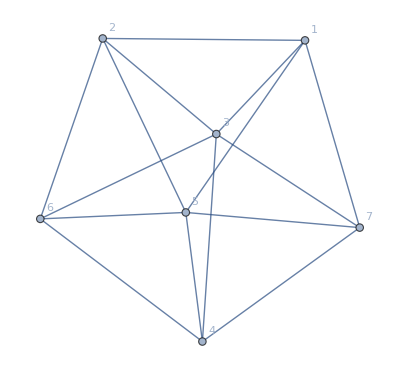
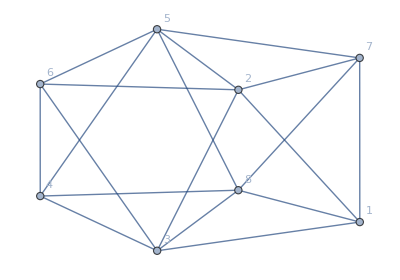
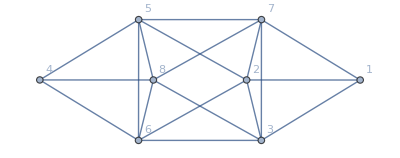
{0,0,-Graphics-3,0,0,-Graphics-6,-Graphics-7,0,0,0,0,0,0,0,0,0,0,-Graphics-18,-Graphics-19,0}

```mathematica
Table[If[Max[VertexDegree[ReadGrof[k]]]==5,Labeled[Graph[ReadGrof[k],VertexLabels->"Name"],k],0],{k,20}]
```

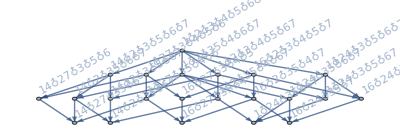
{-Graphics-,{v14x27x3x5x6,v14x2x35x6x7,v1x27x35x4x6,v14x2x3x5x67,v1x2x35x4x67,v16x24x3x5x7,v16x2x35x4x7,v1x24x35x6x7,v16x27x3x4x5,v1x24x3x5x67},{v14x27x35x6,v14x2x35x67,v16x24x35x7,v16x27x35x4,v1x24x35x67},-Graphics-}

```mathematica
With[{g=ReadGrof[7]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[  Graph[DrawNormal[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,Select[EdgeList[g],#[[1]]==3||#[[2]]==3&]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
  ],
GraphHighlightStyle->"Thick",
ImageSize->800
,VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]
```

```mathematica
With[{g=ReadGrof[18]},
Select[EdgeList[g],#[[1]]==2||#[[2]]==2&]
]
```

{1<->2,2<->3,2<->5,2<->6,2<->7}

```mathematica
With[{g=ReadGrof[18]},
With[{full=FindFullFormula[g]},
Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[  Graph[DrawNormal[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,Select[EdgeList[g],#[[1]]==2||#[[2]]==2&]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
  ],
GraphHighlightStyle->"Thick",
ImageSize->1600
,VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
]
]
```

-Graphics-

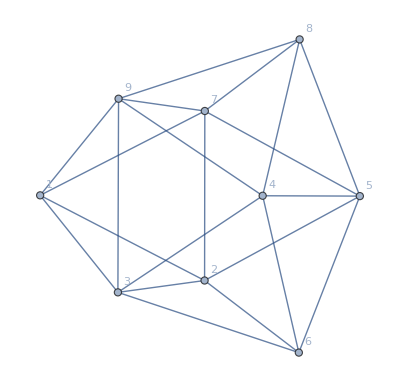
{0,0,-Graphics-3,0,0,-Graphics-6,0,0,0,0,0,0,0,0,0,0,0,-Graphics-18,-Graphics-19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Graphics-46,0,0,0,0}

```mathematica
Table[With[{g=ReadGrof[k]},
If[Max[VertexDegree[g]]==5&&ChromaticPolynomial[g,4]<100,Labeled[Graph[g,VertexLabels->"Name"],k],0]],{k,50}]
```

```mathematica
FinerSyms[s_]:=Select[Map[SetsToSymbol,FindFiner[SymbolToSets[s]]],#=!=s&]
```

```mathematica
CoarserSyms[s_]:=Select[Map[SetsToSymbol,FindCoarser[SymbolToSets[s]]],#=!=s&]
```

```mathematica
With[{g=ReadGrof[46]},
With[{full5=FindFullFormula5[g],
full4=FindFullFormula4[g]
},
With[
{good=Flatten[Table[AugmentedFormula[FindFullFormula4[EdgeContract[g,e]],e,full5],{e,Select[EdgeList[g],#[[1]]==2||#[[2]]==2&]}]]},
Print[good];
Print[full4];
Table[If[SubsetQ[good,FinerSyms[atom]],atom,Null],{atom,full4}]
]
]
]
```

{v1x24x38x59x67,v14x2x38x59x67,v1x28x35x47x69,v18x2x35x47x69,v1x24x37x59x68,v14x2x37x59x68,v14x2x38x59x67,v14x28x3x59x67,v168x2x3x47x59,v16x2x38x47x59,v16x28x3x47x59,v15x2x38x47x69,v15x28x3x47x69,v14x2x38x59x67,v14x29x38x5x67,v14x2x37x59x68,v14x29x37x5x68,v168x2x3x47x59,v168x29x3x47x5,v16x2x38x47x59,v16x29x38x47x5,v168x2x37x4x59,v168x29x37x4x5,v18x2x35x47x69,v18x29x35x47x6,v14x2x37x59x68,v14x28x37x59x6,v15x2x38x47x69,v15x29x38x47x6,v18x2x35x47x69,v18x24x35x69x7,v168x2x3x47x59,v168x24x3x59x7,v16x2x38x47x59,v16x24x38x59x7,v168x2x35x47x9,v168x24x35x7x9,v15x2x38x47x69,v15x24x38x69x7}

{v168x24x37x59,v168x29x35x47}

{Null,Null}

```mathematica
Map[SymbolLevel,CoarserSyms[v1x24x38x59x67]]
```

{4,4,4,4,4,4,4,4,4,4}

```mathematica
SubsetQ[{v1x24x37x59x68,v16x24x37x59x8,v18x24x37x59x6,v168x2x37x4x59,v168x24x3x59x7,v168x24x37x5x9},FinerSyms[v168x24x37x59]]
```

True

```mathematica
With[{g=ReadGrof[46]},
With[{full5=FindFullFormula5[g],
full4=FindFullFormula4[g]
},
With[
{good=Flatten[Table[AugmentedFormula[FindFullFormula4[EdgeContract[g,e]],e,full5],{e,EdgeList[g]}]]},
Table[If[SubsetQ[good,FinerSyms[atom]],atom,"Miep"],{atom,full4}]
]
]
]
```

{v168x24x37x59,v168x29x35x47}

```mathematica
Monitor[Table[With[{g=ReadGrof[gr]},
With[{full5=FindFullFormula5[g],
full4=FindFullFormula4[g]
},
With[
{good=Flatten[Table[AugmentedFormula[FindFullFormula4[GContract[g,e]],e,full5],{e,EdgeList[g]}]]},
Table[If[SubsetQ[good,FinerSyms[atom]],atom,{good,Style[atom,Red]}],{atom,full4}]
]
]
],
{gr,15,20}
],
gr]
```

{{v15x24x38x67,{{v1x25x3x48x67,v15x2x3x48x67,v1x25x38x47x6,v15x2x38x47x6,v1x25x38x4x67,v15x2x38x4x67,v1x24x38x5x67,v14x2x38x5x67,v1x25x38x47x6,v18x25x3x47x6,v1x25x38x4x67,v18x25x3x4x67,v1x25x3x48x67,v1x24x38x5x67,v18x24x3x5x67,v1x25x3x48x67,v16x25x3x48x7,v1x25x38x47x6,v14x25x38x6x7,v1x25x38x4x67,v16x25x38x4x7,v1x24x38x5x67,v16x24x38x5x7,v15x2x3x48x67,v148x2x3x5x67,v15x2x38x47x6,v15x2x38x47x6,v15x24x38x6x7,v16x2x38x47x5,v16x24x38x5x7,v15x2x3x48x67,v15x24x3x67x8,v1x25x3x48x67,v1x25x38x4x67,v15x2x3x48x67,v15x2x38x4x67,v18x25x3x4x67,v16x25x3x48x7,v16x25x38x4x7,v148x2x3x5x67,v18x24x3x5x67,v148x25x3x6x7,v18x25x3x47x6,v148x25x3x6x7,v16x25x3x48x7,v1x25x38x4x67,v1x24x38x5x67,v15x2x38x4x67,v14x2x38x5x67,v18x25x3x4x67,v18x24x3x5x67,v16x25x38x4x7,v16x24x38x5x7,v1x25x38x47x6,v1x25x38x4x67,v14x25x38x6x7,v16x25x38x4x7,v15x2x38x47x6,v15x2x38x4x67,v18x25x3x47x6,v18x25x3x4x67,v15x2x38x47x6,v16x2x38x47x5,v15x24x38x6x7,v16x24x38x5x7,v16x24x38x5x7,v15x24x3x67x8,v18x24x3x5x67,v18x25x3x47x6,v16x25x3x47x8,v16x25x3x48x7,v16x25x3x47x8},v14x25x38x67},{{v1x25x3x48x67,v15x2x3x48x67,v1x25x38x47x6,v15x2x38x47x6,v1x25x38x4x67,v15x2x38x4x67,v1x24x38x5x67,v14x2x38x5x67,v1x25x38x47x6,v18x25x3x47x6,v1x25x38x4x67,v18x25x3x4x67,v1x25x3x48x67,v1x24x38x5x67,v18x24x3x5x67,v1x25x3x48x67,v16x25x3x48x7,v1x25x38x47x6,v14x25x38x6x7,v1x25x38x4x67,v16x25x38x4x7,v1x24x38x5x67,v16x24x38x5x7,v15x2x3x48x67,v148x2x3x5x67,v15x2x38x47x6,v15x2x38x47x6,v15x24x38x6x7,v16x2x38x47x5,v16x24x38x5x7,v15x2x3x48x67,v15x24x3x67x8,v1x25x3x48x67,v1x25x38x4x67,v15x2x3x48x67,v15x2x38x4x67,v18x25x3x4x67,v16x25x3x48x7,v16x25x38x4x7,v148x2x3x5x67,v18x24x3x5x67,v148x25x3x6x7,v18x25x3x47x6,v148x25x3x6x7,v16x25x3x48x7,v1x25x38x4x67,v1x24x38x5x67,v15x2x38x4x67,v14x2x38x5x67,v18x25x3x4x67,v18x24x3x5x67,v16x25x38x4x7,v16x24x38x5x7,v1x25x38x47x6,v1x25x38x4x67,v14x25x38x6x7,v16x25x38x4x7,v15x2x38x47x6,v15x2x38x4x67,v18x25x3x47x6,v18x25x3x4x67,v15x2x38x47x6,v16x2x38x47x5,v15x24x38x6x7,v16x24x38x5x7,v16x24x38x5x7,v15x24x3x67x8,v18x24x3x5x67,v18x25x3x47x6,v16x25x3x47x8,v16x25x3x48x7,v16x25x3x47x8},v148x25x3x67},v16x25x38x47},{v158x24x3x67},{v15x24x38x67},{v14x28x35x67,v16x28x35x47,v15x24x37x68},{v14x28x35x67,v18x24x35x67,v16x28x35x47,v15x28x34x67},{v14x25x37x68,{{v1x24x37x5x68,v14x2x37x5x68,v1x25x3x47x68,v1x25x3x478x6,v1x24x37x5x68,v1x248x37x5x6,v1x25x3x47x68,v14x25x3x68x7,v1x24x37x5x68,v16x24x37x5x8,v1x25x3x47x68,v16x25x3x47x8,v1x25x37x48x6,v14x25x37x6x8,v1x25x37x4x68,v16x25x37x4x8,v16x2x3x478x5,v14x2x37x5x68,v14x28x37x5x6,v16x2x3x478x5,v16x24x3x5x78,v16x248x3x5x7,v16x28x3x47x5,v1x25x3x47x68,v1x25x37x4x68,v16x28x3x47x5,v16x28x37x4x5,v16x25x3x47x8,v16x25x37x4x8,v16x25x3x4x78,v16x2x3x478x5,v16x24x3x5x78,v16x248x3x5x7,v16x28x3x47x5,v1x25x3x478x6,v14x25x3x6x78,v14x25x3x6x78,v14x25x37x6x8,v16x24x3x5x78,v16x24x37x5x8,v16x25x3x4x78,v16x25x37x4x8,v16x25x3x47x8,v1x24x37x5x68,v1x25x37x4x68,v16x24x3x5x78,v16x25x3x4x78,v16x24x37x5x8,v16x25x37x4x8,v16x28x37x4x5,v1x25x37x48x6,v1x25x37x4x68,v14x28x37x5x6,v16x28x37x4x5,v14x25x3x6x78,v16x25x3x4x78,v14x25x37x6x8,v16x25x37x4x8,v1x248x37x5x6,v14x28x37x5x6,v16x248x3x5x7,v14x28x37x5x6,v14x25x37x6x8,v16x28x3x47x5,v16x25x3x47x8,v16x28x37x4x5,v16x25x37x4x8,v16x24x37x5x8,v14x25x3x68x7,v14x25x3x6x78},v16x248x37x5},{{v1x24x37x5x68,v14x2x37x5x68,v1x25x3x47x68,v1x25x3x478x6,v1x24x37x5x68,v1x248x37x5x6,v1x25x3x47x68,v14x25x3x68x7,v1x24x37x5x68,v16x24x37x5x8,v1x25x3x47x68,v16x25x3x47x8,v1x25x37x48x6,v14x25x37x6x8,v1x25x37x4x68,v16x25x37x4x8,v16x2x3x478x5,v14x2x37x5x68,v14x28x37x5x6,v16x2x3x478x5,v16x24x3x5x78,v16x248x3x5x7,v16x28x3x47x5,v1x25x3x47x68,v1x25x37x4x68,v16x28x3x47x5,v16x28x37x4x5,v16x25x3x47x8,v16x25x37x4x8,v16x25x3x4x78,v16x2x3x478x5,v16x24x3x5x78,v16x248x3x5x7,v16x28x3x47x5,v1x25x3x478x6,v14x25x3x6x78,v14x25x3x6x78,v14x25x37x6x8,v16x24x3x5x78,v16x24x37x5x8,v16x25x3x4x78,v16x25x37x4x8,v16x25x3x47x8,v1x24x37x5x68,v1x25x37x4x68,v16x24x3x5x78,v16x25x3x4x78,v16x24x37x5x8,v16x25x37x4x8,v16x28x37x4x5,v1x25x37x48x6,v1x25x37x4x68,v14x28x37x5x6,v16x28x37x4x5,v14x25x3x6x78,v16x25x3x4x78,v14x25x37x6x8,v16x25x37x4x8,v1x248x37x5x6,v14x28x37x5x6,v16x248x3x5x7,v14x28x37x5x6,v14x25x37x6x8,v16x28x3x47x5,v16x25x3x47x8,v16x28x37x4x5,v16x25x37x4x8,v16x24x37x5x8,v14x25x3x68x7,v14x25x3x6x78},v16x25x3x478},{{v1x24x37x5x68,v14x2x37x5x68,v1x25x3x47x68,v1x25x3x478x6,v1x24x37x5x68,v1x248x37x5x6,v1x25x3x47x68,v14x25x3x68x7,v1x24x37x5x68,v16x24x37x5x8,v1x25x3x47x68,v16x25x3x47x8,v1x25x37x48x6,v14x25x37x6x8,v1x25x37x4x68,v16x25x37x4x8,v16x2x3x478x5,v14x2x37x5x68,v14x28x37x5x6,v16x2x3x478x5,v16x24x3x5x78,v16x248x3x5x7,v16x28x3x47x5,v1x25x3x47x68,v1x25x37x4x68,v16x28x3x47x5,v16x28x37x4x5,v16x25x3x47x8,v16x25x37x4x8,v16x25x3x4x78,v16x2x3x478x5,v16x24x3x5x78,v16x248x3x5x7,v16x28x3x47x5,v1x25x3x478x6,v14x25x3x6x78,v14x25x3x6x78,v14x25x37x6x8,v16x24x3x5x78,v16x24x37x5x8,v16x25x3x4x78,v16x25x37x4x8,v16x25x3x47x8,v1x24x37x5x68,v1x25x37x4x68,v16x24x3x5x78,v16x25x3x4x78,v16x24x37x5x8,v16x25x37x4x8,v16x28x37x4x5,v1x25x37x48x6,v1x25x37x4x68,v14x28x37x5x6,v16x28x37x4x5,v14x25x3x6x78,v16x25x3x4x78,v14x25x37x6x8,v16x25x37x4x8,v1x248x37x5x6,v14x28x37x5x6,v16x248x3x5x7,v14x28x37x5x6,v14x25x37x6x8,v16x28x3x47x5,v16x25x3x47x8,v16x28x37x4x5,v16x25x37x4x8,v16x24x37x5x8,v14x25x3x68x7,v14x25x3x6x78},v16x25x37x48}}}

```mathematica
.;;
```

```mathematica
Intersection[{v1x25x3x48x67,v15x2x3x48x67,v1x25x38x47x6,v15x2x38x47x6,v1x25x38x4x67,v15x2x38x4x67,v1x24x38x5x67,v14x2x38x5x67,v1x25x38x47x6,v18x25x3x47x6,v1x25x38x4x67,v18x25x3x4x67,v1x25x3x48x67,v1x24x38x5x67,v18x24x3x5x67,v1x25x3x48x67,v16x25x3x48x7,v1x25x38x47x6,v14x25x38x6x7,v1x25x38x4x67,v16x25x38x4x7,v1x24x38x5x67,v16x24x38x5x7,v15x2x3x48x67,v148x2x3x5x67,v15x2x38x47x6,v15x2x38x47x6,v15x24x38x6x7,v16x2x38x47x5,v16x24x38x5x7,v15x2x3x48x67,v15x24x3x67x8,v1x25x3x48x67,v1x25x38x4x67,v15x2x3x48x67,v15x2x38x4x67,v18x25x3x4x67,v16x25x3x48x7,v16x25x38x4x7,v148x2x3x5x67,v18x24x3x5x67,v148x25x3x6x7,v18x25x3x47x6,v148x25x3x6x7,v16x25x3x48x7,v1x25x38x4x67,v1x24x38x5x67,v15x2x38x4x67,v14x2x38x5x67,v18x25x3x4x67,v18x24x3x5x67,v16x25x38x4x7,v16x24x38x5x7,v1x25x38x47x6,v1x25x38x4x67,v14x25x38x6x7,v16x25x38x4x7,v15x2x38x47x6,v15x2x38x4x67,v18x25x3x47x6,v18x25x3x4x67,v15x2x38x47x6,v16x2x38x47x5,v15x24x38x6x7,v16x24x38x5x7,v16x24x38x5x7,v15x24x3x67x8,v18x24x3x5x67,v18x25x3x47x6,v16x25x3x47x8,v16x25x3x48x7,v16x25x3x47x8},FinerSyms[v14x25x38x67]]
```

{v14x25x38x6x7,v14x2x38x5x67,v1x25x38x4x67}

```mathematica
FinerSyms[v14x25x38x67]
```

{v1x25x38x4x67,v14x2x38x5x67,v14x25x3x67x8,v14x25x38x6x7}

```mathematica
Monitor[Table[With[{g=ReadGrof[gr]},
With[{full5=FindFullFormula5[g],
full4=FindFullFormula4[g]
},
With[
{good=Flatten[Table[AugmentedFormula[FindFullFormula4[GContract[g,e]],e,full5],{e,EdgeList[GraphComplement[g]]}]]},
Table[If[SubsetQ[good,FinerSyms[atom]],atom,{good,Style[atom,Red]}],{atom,full4}]
]
]
],
{gr,15,50}
],
gr]
```

{{v15x24x38x67,v14x25x38x67,v148x25x3x67,v16x25x38x47},{v158x24x3x67},{v15x24x38x67},{v14x28x35x67,v16x28x35x47,v15x24x37x68},{v14x28x35x67,v18x24x35x67,v16x28x35x47,v15x28x34x67},{v14x25x37x68,v16x248x37x5,v16x25x3x478,v16x25x37x48},{v1x267x35x48,v16x24x35x78,v16x27x35x48,v14x26x35x78,v14x267x35x8,v148x2x35x67,v148x26x35x7,v18x24x35x67,v148x267x3x5,v18x267x35x4,v148x27x35x6},{v178x246x3x5},{v16x24x38x57},{v15x26x34x789},{v159x24x36x78,v159x28x34x67,v159x28x36x47,v15x28x36x479},{v156x2x34x789,v156x24x3x789,v156x24x39x78,v156x28x34x79,v156x28x39x47},{v145x28x39x67},{v15x28x39x467},{v167x28x34x59},{v16x278x349x5,v15x28x349x67,v15x278x34x69,v15x278x349x6},{v149x28x35x67,v18x249x35x67,v169x24x35x78,v16x249x35x78,v169x28x35x47},{v159x28x34x67},{v15x28x349x67},{v15x289x34x67},{v156x24x39x78,v156x28x34x79,v156x28x39x47,v145x28x39x67},{v189x25x34x67,v156x24x39x78,v156x28x39x47},{v1x268x35x479,v18x26x35x479,v168x2x35x479,v16x28x35x479,v168x24x35x79,v14x268x35x79,v149x28x35x67,v149x268x35x7,v19x268x35x47,v189x26x35x47,v189x24x35x67,v15x268x3x479},{v189x24x35x67,v168x24x35x79,v159x28x36x47},{v147x2x35x689,v147x28x35x69,v17x24x35x689,v167x28x35x49,v167x24x35x89},{v1x247x35x689,v18x247x35x69,v14x27x35x689,v168x247x35x9,v16x247x35x89,v168x27x35x49,v168x247x39x5,v15x247x3x689,v15x247x39x68},{v18x249x35x67,v168x24x37x59,v168x249x35x7,v168x29x35x47,v168x249x37x5,v15x249x37x68},{v149x28x35x67,v189x24x35x67,v168x2x35x479,v16x28x35x479,v168x24x35x79},{v189x24x35x67,v14x289x35x67,v168x29x35x47,v16x289x35x47,v168x24x35x79},{v149x28x35x67,v189x24x35x67,v168x2x35x479,v16x28x35x479,v168x24x35x79},{v149x28x35x67,v189x24x35x67,v1689x2x35x47,v169x28x35x47,v1689x24x35x7},{v168x24x37x59,v168x29x35x47},{v145x26x3x789},{v159x28x3x467},{v18x245x39x67,v145x28x39x67,v189x245x3x67,v16x245x39x78},{v167x28x3x459}}

```mathematica
Monitor[Table[With[{g=ReadGrof[gr]},
With[{full5=FindFullFormula5[g],
full4=FindFullFormula4[g]
},
With[
{good=Flatten[Table[AugmentedFormula[FindFullFormula4[GContract[g,e]],e,full5],{e,EdgeList[GraphComplement[g]]}]]},
Table[If[SubsetQ[good,FinerSyms[atom]],atom,{good,Style[atom,Red]}],{atom,full4}]
]
]
],
{gr,51,100}
],
gr]
```